# Three Flavor vacuum

(0.82362 | 0.544051 | 0.160182
-0.508074 | 0.582297 | 0.634658
0.252012 | -0.604101 | 0.75601)

{0.200786 Re[Sin[0.000096393 x]^2],0.0174054 Re[Sin[0.0029464 x]^2],0.00759465 Re[Sin[0.0029464 x]^2]}

0.200786 Re[Sin[0.000096393 x]^2]+0.025 Re[Sin[0.0029464 x]^2]

0.200786 Im[Sin[0.000096393 x]^2]+0.025 Im[Sin[0.0029464 x]^2]

{0.200786 Im[Sin[0.000096393 x]^2],0.0174054 Im[Sin[0.0029464 x]^2],0.00759465 Im[Sin[0.0029464 x]^2]}

1+2 (0.200786 Im[Sin[0.000096393 LE]^2]+0.025 Im[Sin[0.0029464 LE]^2])-4 (0.200786 Re[Sin[0.000096393 LE]^2]+0.025 Re[Sin[0.0029464 LE]^2])

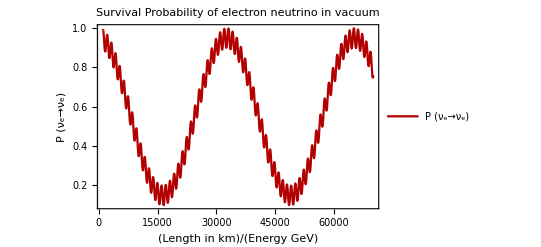

```mathematica
M11=M22=M33=0;
M12=M21=0.759* 10^-4;
M13=M31=M23=M32=23.2*10^−4;
M={{M11,M12,M13},{M21,M22,M23},{M31,M32,M33}};
M//MatrixForm;


theta12=0.5*ArcSin[Sqrt[0.846]];                                                (*Arbitrary 1 sec= 10^-6 radian *)          
theta13=0.5*ArcSin[Sqrt[0.10]];    
theta23=0.5*ArcSin[Sqrt[0.97]];  
                                                                                                                                                           (*Arbitrary 1 sec= 10^-6 radian *)   
phase1=Exp[I*0];
phase2=Exp[I*0];
phase3=Exp[I*0];
Phase={{1,0,0},{0,phase1,0},{0,0,phase2}};
Phase//MatrixForm;

U23={{1,0,0},{0, Cos[theta23],Sin[theta23]},{0,-Sin[theta23],Cos[theta23]}};
U23//MatrixForm;
U13={{Cos[theta13],0,Sin[theta13]},{0,1,0},{-Sin[theta13],0,Cos[theta13]}};
U13//MatrixForm;
U12={{Cos[theta12],Sin[theta12],0},{-Sin[theta12],Cos[theta12],0},{0,0,1}};
U12//MatrixForm;




U=U23.U13.U12.Phase;
U//MatrixForm




alpha=1;
beta=1;
Nmax=3;
x=Symbol["x"];                                                                (*define a variable x*)
list1={};                                                                               (*define an empty list*)
For[i=1,i<Nmax,i++,
For[j=i+1,j<=Nmax,j++,
prod=(U[[alpha,i]]*Conjugate[U[[beta,i]]]*Conjugate[U[[alpha,j]]]*U[[beta,j]])*Sin[1.27*M[[i,j]]*x]^2;
realpart= Re[prod];
AppendTo[list1,realpart];
]
]
list1
sumReal[x_]=Total[list1]
                                                                                                    
list2={};                                                                               (*define an empty list to collect imaginary part*)
For[i=1,i<Nmax,i++,
For[j=i+1,j<=Nmax,j++,
prod=(U[[alpha,i]]*Conjugate[U[[beta,i]]]*Conjugate[U[[alpha,j]]]*U[[beta,j]])*Sin[1.27*M[[i,j]]*x]^2;
impart= Im[prod];
AppendTo[list2,impart];
]
]
sumIm[x_]=Total[list2]
list2

Peu[LE_]:=If[alpha==beta,1,0]-4*sumReal[LE]+2*sumIm[LE];
Peu[LE]
P1=Plot[Peu[LE],{LE,1000,70000},PlotRange->Full, PlotLabel->"Survival Probability of electron neutrino in vacuum",
PlotLegends->{"P (ν_e→ν_e)"},PlotTheme-> "Scientific", PlotStyle->Directive[RGBColor[0.7,0,0]],FrameLabel->{{HoldForm[P (Subscript[ν, e]->Subscript[ν, e])],None},{HoldForm[Length/Energy in km/GeV],None}}]
```

(0 | 0.0000759 | 0.00232
0.0000759 | 0 | 0.00232
0.00232 | 0.00232 | 0)

(0.82362 | 0.544051 | 0.160182
-0.508074 | 0.582297 | 0.634658
0.252012 | -0.604101 | 0.75601)

2 (-0.132568 Im[Sin[0.000096393 LE]^2]-0.0103349 Im[Sin[0.0029464 LE]^2])-4 (-0.132568 Re[Sin[0.000096393 LE]^2]-0.0103349 Re[Sin[0.0029464 LE]^2])

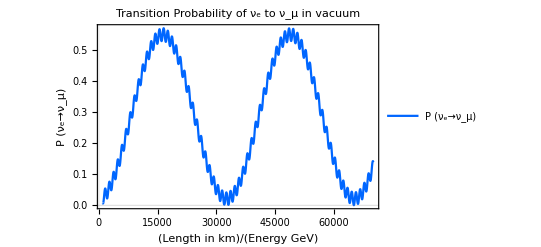

```mathematica
M11=M22=M33=0;
M12=M21=0.759* 10^-4;
M13=M31=M23=M32=23.2*10^−4;
M={{M11,M12,M13},{M21,M22,M23},{M31,M32,M33}};
M//MatrixForm


theta12=0.5*ArcSin[Sqrt[0.846]];                                                (*Arbitrary 1 sec= 10^-6 radian *)          
theta13=0.5*ArcSin[Sqrt[0.10]];    
theta23=0.5*ArcSin[Sqrt[0.97]];  
                                                                                                                                                           (*Arbitrary 1 sec= 10^-6 radian *)   
phase1=Exp[I*0];
phase2=Exp[I*0];
phase3=Exp[I*0];
Phase={{1,0,0},{0,phase1,0},{0,0,phase2}};
Phase//MatrixForm;

U23={{1,0,0},{0, Cos[theta23],Sin[theta23]},{0,-Sin[theta23],Cos[theta23]}};
U23//MatrixForm;
U13={{Cos[theta13],0,Sin[theta13]},{0,1,0},{-Sin[theta13],0,Cos[theta13]}};
U13//MatrixForm;
U12={{Cos[theta12],Sin[theta12],0},{-Sin[theta12],Cos[theta12],0},{0,0,1}};
U12//MatrixForm;

U=U23.U13.U12.Phase;
U//MatrixForm

alpha=1;
beta=2;
Nmax=3;
x=Symbol["x"];                                                                (*define a variable x*)
list1={};                                                                               (*define an empty list*)
For[i=1,i<Nmax,i++,
For[j=i+1,j<=Nmax,j++,
prod=(U[[alpha,i]]*Conjugate[U[[beta,i]]]*Conjugate[U[[alpha,j]]]*U[[beta,j]])*Sin[1.27*M[[i,j]]*x]^2;
realpart= Re[prod];
AppendTo[list1,realpart];
]
]
sumReal[x_]=Total[list1];
                                                                                                    
list2={};                                                                               (*define an empty list to collect imaginary part*)
For[i=1,i<Nmax,i++,
For[j=i+1,j<=Nmax,j++,
prod=(U[[alpha,i]]*Conjugate[U[[beta,i]]]*Conjugate[U[[alpha,j]]]*U[[beta,j]])*Sin[1.27*M[[i,j]]*x]^2;
impart= Im[prod];
AppendTo[list2,impart];
]
]
sumIm[x_]=Total[list2];


Peu[LE_]:=If[alpha==beta,1,0]-4*sumReal[LE]+2*sumIm[LE];
Peu[LE]
P2=Plot[Peu[LE],{LE,1000,70000},PlotRange->Full, PlotLabel->"Transition Probability of ν_e to ν_μ in vacuum",
PlotLegends->{"P (ν_e→ν_μ)"},PlotStyle->Directive[Hue[0.6]],PlotTheme-> "Scientific", FrameLabel->{{HoldForm[P (Subscript[ν, e]->Subscript[ν, μ])],None},{HoldForm[Length/Energy in km/GeV],None}}]
```

(0 | 0.0000759 | 0.00232
0.0000759 | 0 | 0.00232
0.00232 | 0.00232 | 0)

(0.82362 | 0.544051 | 0.160182
-0.508074 | 0.582297 | 0.634658
0.252012 | -0.604101 | 0.75601)

2 (-0.0682178 Im[Sin[0.000096393 LE]^2]-0.0146651 Im[Sin[0.0029464 LE]^2])-4 (-0.0682178 Re[Sin[0.000096393 LE]^2]-0.0146651 Re[Sin[0.0029464 LE]^2])

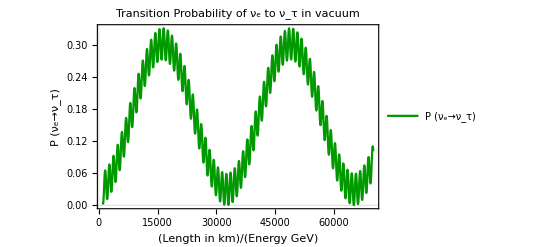

```mathematica
M11=M22=M33=0;
M12=M21=0.759* 10^-4;
M13=M31=M23=M32=23.2*10^−4;
M={{M11,M12,M13},{M21,M22,M23},{M31,M32,M33}};
M//MatrixForm


theta12=0.5*ArcSin[Sqrt[0.846]];                                                (*Arbitrary 1 sec= 10^-6 radian *)          
theta13=0.5*ArcSin[Sqrt[0.10]];    
theta23=0.5*ArcSin[Sqrt[0.97]];  
                                                                                                                                                           (*Arbitrary 1 sec= 10^-6 radian *)   
phase1=Exp[I*0];
phase2=Exp[I*0];
phase3=Exp[I*0];
Phase={{1,0,0},{0,phase1,0},{0,0,phase2}};
Phase//MatrixForm;

U23={{1,0,0},{0, Cos[theta23],Sin[theta23]},{0,-Sin[theta23],Cos[theta23]}};
U23//MatrixForm;
U13={{Cos[theta13],0,Sin[theta13]},{0,1,0},{-Sin[theta13],0,Cos[theta13]}};
U13//MatrixForm;
U12={{Cos[theta12],Sin[theta12],0},{-Sin[theta12],Cos[theta12],0},{0,0,1}};
U12//MatrixForm;

U=U23.U13.U12.Phase;
U//MatrixForm

alpha=1;
beta=3;
Nmax=3;
x=Symbol["x"];                                                                (*define a variable x*)
list1={};                                                                               (*define an empty list*)
For[i=1,i<Nmax,i++,
For[j=i+1,j<=Nmax,j++,
prod=(U[[alpha,i]]*Conjugate[U[[beta,i]]]*Conjugate[U[[alpha,j]]]*U[[beta,j]])*Sin[1.27*M[[i,j]]*x]^2;
realpart= Re[prod];
AppendTo[list1,realpart];
]
]
sumReal[x_]=Total[list1];
                                                                                                    
list2={};                                                                               (*define an empty list to collect imaginary part*)
For[i=1,i<Nmax,i++,
For[j=i+1,j<=Nmax,j++,
prod=(U[[alpha,i]]*Conjugate[U[[beta,i]]]*Conjugate[U[[alpha,j]]]*U[[beta,j]])*Sin[1.27*M[[i,j]]*x]^2;
impart= Im[prod];
AppendTo[list2,impart];
]
]
sumIm[x_]=Total[list2];


Peu[LE_]:=If[alpha==beta,1,0]-4*sumReal[LE]+2*sumIm[LE];
Peu[LE]
P3=Plot[Peu[LE],{LE,1000,70000},PlotRange->Full, PlotLabel->"Transition Probability of ν_e to ν_τ in vacuum",
 PlotLegends->{"P (ν_e→ν_τ)"},PlotStyle->Directive[RGBColor[0,0.6,0]],PlotTheme-> "Scientific", FrameLabel->{{HoldForm[P (Subscript[ν, e]->Subscript[ν, τ])],None},{HoldForm[Length/Energy in km/GeV],None}}]
```

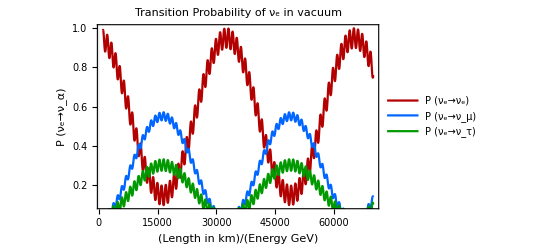

```mathematica
Show[P1,P2,P3,PlotLabel->"Transition Probability of ν_e in vacuum",FrameLabel->{{HoldForm[P (Subscript[ν, e]->Subscript[ν, α])],None},{HoldForm[Length/Energy in km/GeV],None}}]
```